```mathematica
ζ[a_,b_]:=N[BesselJZero[a+1/2,b]];
```

```mathematica
B[ν_,μ_,n_]:=(2*3/μ*NIntegrate[LegendreQ[ν,μ,z],{z,0,1}]*NIntegrate[r^2*SphericalBesselJ[ν,ζ[ν,n]*r],{r,0,1}])/(π*NIntegrate[LegendreQ[ν,μ,z]^2,{z,0,1}]*NIntegrate[r^2*SphericalBesselJ[ν,ζ[ν,n]*r]^2,{r,0,1}]);
```

```mathematica
B[5/2, 3/2, 2]
```

14.7507

```mathematica
nmax=10;
νmax=8;
μmax=10;
```

```mathematica
T[r_,z_,ϕ_,t_]:=Sum[Sum[Sum[B[ν,μ,n]*LegendreQ[ν,μ,z]*Sin[ν*ϕ]*SphericalBesselJ[ν,ζ[ν,n]*r]*ⅇ^(-ζ[ν,n]*t),{n,1,nmax,1}],{ν,μ+1,νmax,2}],{μ,5/2,μmax,2*3/2}];
```

```mathematica
T[0.5,0.2,π/3, 0.001]
T[0.5,0.2,π/3, 0.002]
T[0.5,0.2,π/3, 0.003]
T[0.5,0.2,π/3, 0.005]
T[0.5,0.2,π/3, 0.009]
```

0.169799

0.166577

0.163338

0.156832

0.143836

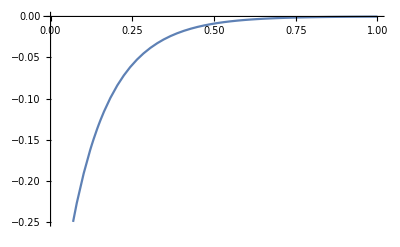

```mathematica
Plot[T[0.5,Cos[π/4],π/3,t],{t, 0,1}]
```

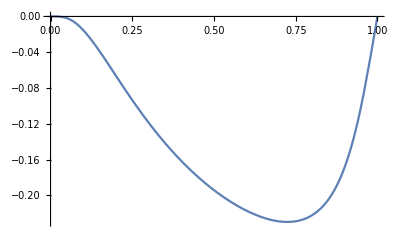

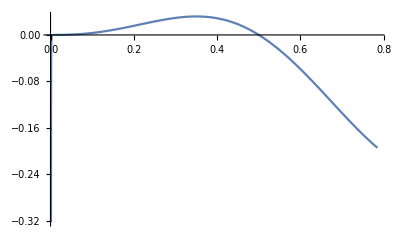

```mathematica
Plot[T[r,Cos[π/4],π/3,0.1],{r, 0,1}]
Plot[T[0.5,Cos[θ],π/3,0.1],{θ, 0,π/4}]
```

```mathematica
For[i=1,i<10,i++,max=FindMaximum[T[r,z,π/3,0.01+i/100],{{r,0.5},{z,0.5}}];Print[max]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.120669,{r→0.453335,z→0.167528}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0880076,{r→0.464436,z→0.159392}}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

{0.110215,{r→0.815466,z→0.167319}}

{0.0959956,{r→0.867684,z→0.1667}}

{0.0815753,{r→0.863552,z→0.163861}}

FindMaximum::nrnum: The function value -0.201976-0.221102 ⅈ is not a real number at {r,z} = {3.71968,1.25766}.

{0.00394436,{r→0.36267,z→0.0607907}}

FindMaximum::nrnum: The function value -6.30536-6.08766 ⅈ is not a real number at {r,z} = {1.2153,1.34317}.

{0.00761856,{r→0.448817,z→0.0725872}}

FindMaximum::nrnum: The function value 0.+0.0169048 ⅈ is not a real number at {r,z} = {-0.243908,-0.0580586}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

{-0.00265968,{r→0.444094,z→-0.0713621}}

{0.0206067,{r→0.434591,z→-0.190006}}

```mathematica
T[0.5,0.5,π/3]
```

T[0.5,0.5,π/3]

```mathematica
testQ[ν_,μ_]:=NIntegrate[LegendreQ[ν,μ,z],{z,0,1}]/NIntegrate[LegendreQ[ν,μ,z]^2,{z,0,1}];
testj[ν_,n_]:=(NIntegrate[r^2*SphericalBesselJ[ν,ζ[ν,n]*r],{r,0,1}])/NIntegrate[r^2*SphericalBesselJ[ν,ζ[ν,n]*r]^2,{r,0,1}];
```

```mathematica
testQ[99/2,9/2]
```

-5.90501×10^-9

```mathematica
testj[3/2,4000]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.912094}. NIntegrate obtained -1.80689×10^-7 and 1.64514×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.916}. NIntegrate obtained 3.1548×10^-9 and 1.25118×10^-10 for the integral and error estimates.

-57.2742

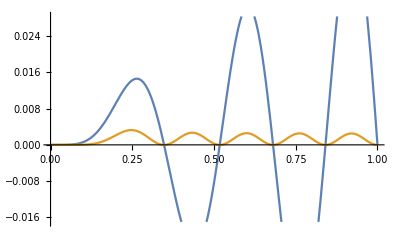

```mathematica
Plot[{r^2*SphericalBesselJ[3,ζ[3,5]*r],r^2*SphericalBesselJ[3,ζ[3,5]*r]^2},{r,0,1}]
```

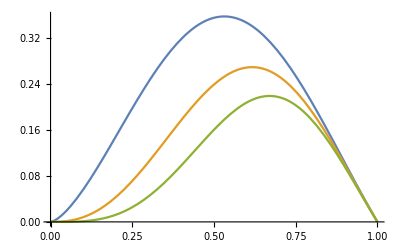

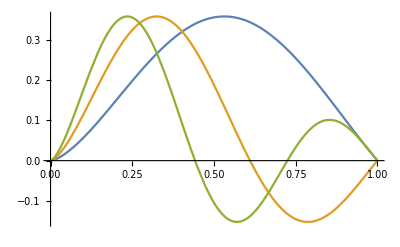

```mathematica
Plot[{SphericalBesselJ[3/2,ζ[3/2,1]*r],SphericalBesselJ[5/2,ζ[5/2,1]*r],SphericalBesselJ[7/2,ζ[7/2,1]*r]},{r,0,1}]
Plot[{SphericalBesselJ[3/2,ζ[3/2,1]*r],SphericalBesselJ[3/2,ζ[3/2,2]*r],SphericalBesselJ[3/2,ζ[3/2,3]*r]},{r,0,1}]
```

```mathematica
LegendreQ[0,0,0.1]
LegendreQ[1,0,0.1]
LegendreQ[0,1,0.1]
LegendreQ[1,1,0.1]
```

0.100335

-0.989966

-1.00504

-0.200336

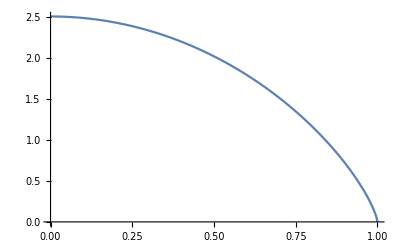

1.94484

```mathematica
Plot[LegendreQ[3/2,3/2,x],{x,1,0}]
LegendreQ[5/2,3/2,0.2]
```

```mathematica
N[f[0]]
```

General::ivar: 0 is not a valid variable.

General::ivar: 0. is not a valid variable.

∂_0. 6.9069×10^-16

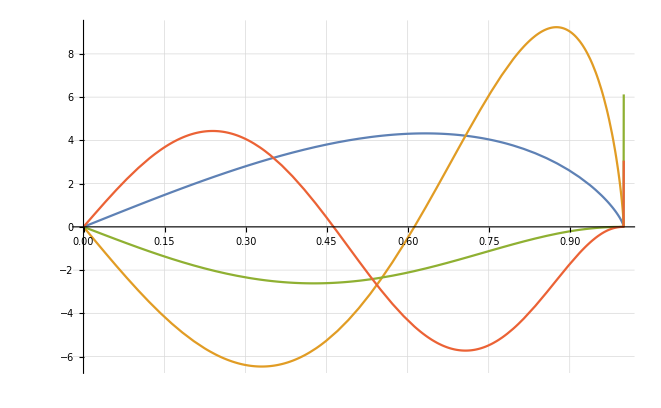

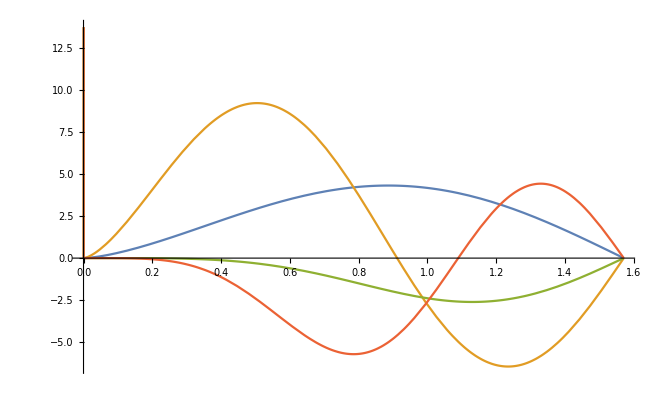

```mathematica
Plot[{LegendreQ[5/2,3/2,z],LegendreQ[9/2,3/2,z],LegendreQ[11/2,9/2,z]/500,LegendreQ[15/2,9/2,z]/1000},{z,0,1},GridLines->Automatic]
Plot[{LegendreQ[5/2,3/2,Cos[θ]],LegendreQ[9/2,3/2,Cos[θ]],LegendreQ[11/2,9/2,Cos[θ]]/500,LegendreQ[15/2,9/2,Cos[θ]]/1000},{θ,0,π/2},GridLines->{{π/6,π/4,2*π/6}, {-1,0,1}}]
```